Energy spectrum of electrons and positrons from burst-like injection (ie, a pulsar), obtained by solving the transport equation.  See Appendix A of arXiv:0905.0636.  Transport parameters taken from Model 0 in Table 1.  Distances are in parsecs, times in seconds, energies in GeV.
Note that the paper includes solar modulation whereas what I have below does not!!!

```mathematica
b0=14*^-17; (* GeV^-1 s^-1 *)
d0=3781*^-12; (* pc^2 s^-1 *)
δ=33*10^-2;
```

```mathematica
e0=1; (* GeV *)
ecut=1100; (* GeV *)
Q0=10^13; (* Arbitrary normalization *)
Δt=6*^4*365*24*3600; (* s *)
Γ=15*10^-1;
c=9716*^-12; (* speed of light in pc/s *)
```

```mathematica
d[e_]:=d0 (e/e0)^δ
```

```mathematica
emax=1/(b0 Δt);
```

```mathematica
rdiff[e_]:=2 √(d[e]Δt(1-(1-e/emax)^(1-δ))/((1-δ)e/emax))
```

```mathematica
dNdE[e_,r_]:=Q0/(π^(3/2) rdiff[e]^3)(1-e/emax)^(Γ-2)(e/(1 (*GeV*)))^-Γ Exp[-e/((1-e/emax)ecut)] Exp[-(r/rdiff[e])^2]*HeavisideTheta[emax-e]
```

```mathematica
aniso[e_,r_]:=(3 d[e])/c(Abs[D[dNdE[e,rd],rd]]//.rd->r)/(4dNdE[e,r]) (* denominator is total density, and N from GCRs is ~3 N from pulsars *)
```

```mathematica
N[aniso[800,290]]
```

0.00569486

```mathematica
N[(dNdE[800,290]*(4+1/2 x aniso[800,290])/.x->1)-(dNdE[800,290]*(4+1/2 x aniso[800,290])/.x->-1)]
```

```mathematica
N[aniso[800,290]*dNdE[800,290]/dNdE[800,290]]
```

0.00569486

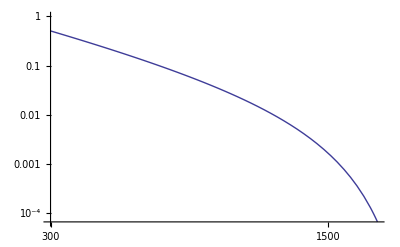

```mathematica
LogLogPlot[dNdE[e,290 (* pc *)],{e,300,2000}]
```

```mathematica
Simplify[Series[dNdE[e,r+Δr]-dNdE[e,r],{Δr,0,1}]]
```